MapThread::mptd: "Object FE`DynamicModuleVariableList$22 at position {2, 1} in MapThread[FrontEnd`Private`settouch, {FE`DynamicModuleVariableList$22, FE`DynamicModuleVariableList$22}] has only 0 of required 1 dimensions."

FE`ExecuteInDynamicModule::noval: Symbol FE`DynamicModuleVariableList$22 does not have a value.

```mathematica
SetDirectory[NotebookDirectory[]];
<<RTNI`
```

Package RTNI (Random Tensor Network Integrator) version 1.0.5 (last modification: 26/01/2019).

Loading precomputed Weingarten Functions from /precomputedWG/functions1.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions2.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions3.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions4.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions5.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions6.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions7.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions8.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions9.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions10.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions11.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions12.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions13.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions14.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions15.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions16.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions17.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions18.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions19.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions20.txt

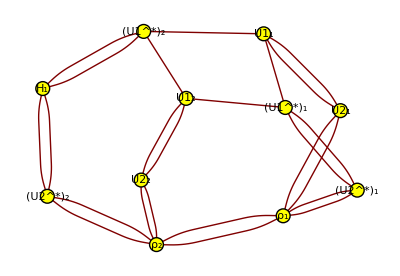

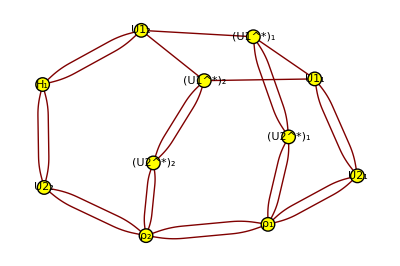

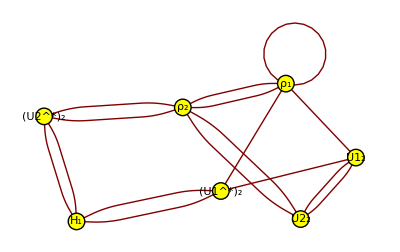

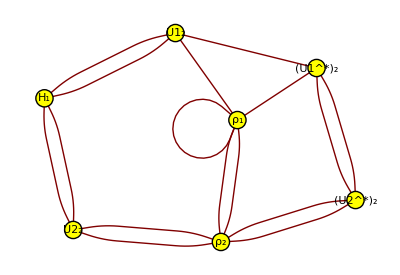

```mathematica
eu1u2A={{"U2",1,"out",1},{"U1",1,"in",1}};
eu1u2B={{"U2",1,"out",2},{"U1",1,"in",2}};
eu2ρ1A={{"ρ",1,"out",2},{"U2",1,"in",1}};
eu2ρ1B={{"ρ",1,"out",3},{"U2",1,"in",2}};
eρ1u2dA ={{"U2*",1,"out",1},{"ρ",1,"in",2}};
eρ1u2dB ={{"U2*",1,"out",2},{"ρ",1,"in",3}};
eu2du1dA={{"U1*",1,"out",1},{"U2*",1,"in",1}};
eu2du1dB={{"U1*",1,"out",2},{"U2*",1,"in",2}};
eu1du1={{"U1",1,"out",2},{"U1*",1,"in",2}};
eu1d2u1={{"U1",2,"out",1},{"U1*",1,"in",1}};

e2u1u2A={{"U2",2,"out",1},{"U1",2,"in",1}};
e2u1u2B={{"U2",2,"out",2},{"U1",2,"in",2}};
e2u2ρ2A={{"ρ",2,"out",2},{"U2",2,"in",1}};
e2u2ρ2B={{"ρ",2,"out",3},{"U2",2,"in",2}};
e2ρ2u2dA ={{"U2*",2,"out",1},{"ρ",2,"in",2}};
e2ρ2u2dB ={{"U2*",2,"out",2},{"ρ",2,"in",3}};
e2u2dHA ={{"H",1,"out",1},{"U2*",2,"in",1}};
e2u2dHB ={{"H",1,"out",2},{"U2*",2,"in",2}};
e2Hu1dA={{"U1*",2,"out",1},{"H",1,"in",1}};
e2Hu1dB={{"U1*",2,"out",2},{"H",1,"in",2}};
e2u1du1={{"U1",2,"out",2},{"U1*",2,"in",2}};
e2u1d2u1={{"U1",1,"out",1},{"U1*",2,"in",1}};
eρ1ρ2={{"ρ",1,"out",1},{"ρ",2,"in",1}};
eρ2ρ1={{"ρ",2,"out",1},{"ρ",1,"in",1}};
tn1={eu1u2A,eu1u2B,eu2ρ1A,eu2ρ1B,eρ1u2dA,eρ1u2dB,eu2du1dA,eu2du1dB,eu1du1,eu1d2u1,e2u1u2A,e2u1u2B,e2u2ρ2A,e2u2ρ2B,e2ρ2u2dA,e2ρ2u2dB,e2u2dHA,e2u2dHB ,e2Hu1dA,e2Hu1dB,e2u1du1,e2u1d2u1,eρ1ρ2,eρ2ρ1};

e2u1HA={{"H",1,"out",1},{"U1",2,"in",1}};
e2u1HB={{"H",1,"out",2},{"U1",2,"in",2}};
e2Hu2A={{"U2",2,"out",1},{"H",1,"in",1}};
e2Hu2B={{"U2",2,"out",2},{"H",1,"in",2}};
e2u2du1dA={{"U1*",2,"out",1},{"U2*",2,"in",1}};
e2u2du1dB={{"U1*",2,"out",2},{"U2*",2,"in",2}};

tn2 ={eu1u2A,eu1u2B,eu2ρ1A,eu2ρ1B,eρ1u2dA,eρ1u2dB,eu2du1dA,eu2du1dB,eu1du1,eu1d2u1,e2u1HA,e2u1HB,e2Hu2A,e2Hu2B,e2u2ρ2A,e2u2ρ2B,e2ρ2u2dA,e2ρ2u2dB,e2u2du1dA,e2u2du1dB,e2u1du1,e2u1d2u1,eρ1ρ2,eρ2ρ1};

eρ1u1A={{"U1",2,"out",1},{"ρ",1,"in",2}};
eu1dρ1A={{"ρ",1,"out",2},{"U1*",2,"in",1}};
eρ1ρ1={{"ρ",1,"out",3},{"ρ",1,"in",3}};
tn3={eρ1u1A,e2u1u2A,e2u1u2B,e2u2ρ2A,e2u2ρ2B,e2ρ2u2dA,e2ρ2u2dB,e2u2dHA,e2u2dHB ,e2Hu1dA,e2Hu1dB,e2u1du1,eu1dρ1A,eρ1ρ2,eρ2ρ1,eρ1ρ1};
tn4 ={eρ1u1A,e2u1HA,e2u1HB,e2Hu2A,e2Hu2B,e2u2ρ2A,e2u2ρ2B,e2ρ2u2dA,e2ρ2u2dB,e2u2du1dA,e2u2du1dB,e2u1du1,eu1dρ1A,eρ1ρ2,eρ2ρ1,eρ1ρ1};

visualizeTN[tn1]
visualizeTN[tn2]
visualizeTN[tn3]
visualizeTN[tn4]
```

```mathematica
tnlist = {{tn1,1},{tn2,-1}};
```

{{{{{ρ,1,out,1},{ρ,2,in,1}},{{ρ,2,out,1},{ρ,1,in,1}},{{ρ,1,out,2},{ρ,1,in,2}},{{ρ,1,out,3},{ρ,1,in,3}},{{ρ,2,out,2},{ρ,2,in,2}},{{ρ,2,out,3},{ρ,2,in,3}},{{H,1,in,1},{H,1,out,1}},{{H,1,in,2},{H,1,out,2}}},d/((-1+d^2) (1+d^2)^2)+d^2/(d+d^3-d^5-d^7)},{{{{ρ,1,out,1},{ρ,2,in,1}},{{ρ,2,out,1},{ρ,1,in,1}},{{ρ,1,out,2},{ρ,2,in,2}},{{ρ,1,out,3},{ρ,2,in,3}},{{ρ,2,out,2},{ρ,1,in,2}},{{ρ,2,out,3},{ρ,1,in,3}},{{H,1,in,1},{H,1,out,1}},{{H,1,in,2},{H,1,out,2}}},1/(d (-1+d^2) (1+d^2)^2)+1/(d+d^3-d^5-d^7)}}

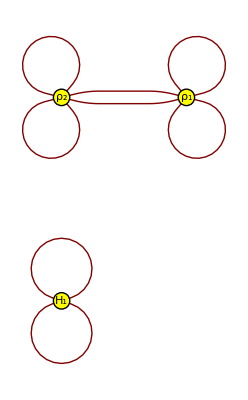
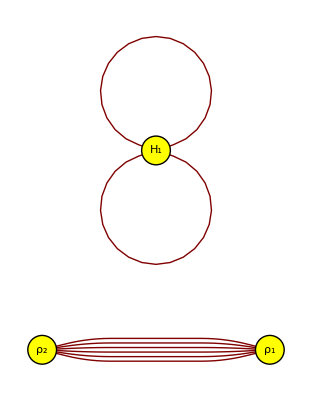
{{-Graphics-,d/((-1+d^2) (1+d^2)^2)+d^2/(d+d^3-d^5-d^7)},{-Graphics-,1/(d (-1+d^2) (1+d^2)^2)+1/(d+d^3-d^5-d^7)}}

```mathematica
EU1tnlist = integrateHaarUnitary[tnlist,"U1",{d,d},{d,d},d *d];
visualizeTN[EU1tnlist];
EU2U1tnlist = integrateHaarUnitary[EU1tnlist,"U2",{d,d},{d,d},d*d]
visualizeTN[EU2U1tnlist]
```

```mathematica
Last[%102]
```

{-Graphics-,1/(d (-1+d^2) (1+d^2)^2)+1/(d+d^3-d^5-d^7)}

```mathematica
tnlist1 ={{tn3,1},{tn4,-1}};
EU1tnlist1 = integrateHaarUnitary[tnlist1,"U1",{d,d},{d,d},d *d];
visualizeTN[EU1tnlist1];
EU2U1tnlist1 = integrateHaarUnitary[EU1tnlist1,"U2",{d,d},{d,d},d*d]
visualizeTN[EU2U1tnlist1]
```

{{{{{ρ,1,out,1},{ρ,2,in,1}},{{ρ,2,out,1},{ρ,1,in,1}},{{ρ,1,out,3},{ρ,1,in,3}},{{ρ,1,in,2},{ρ,1,out,2}},{{ρ,2,out,2},{ρ,2,in,2}},{{ρ,2,out,3},{ρ,2,in,3}},{{H,1,in,1},{H,1,out,1}},{{H,1,in,2},{H,1,out,2}}},0}}

{{-Graphics-,0}}

```mathematica
First[%108]
```

{-Graphics-,0}

```mathematica
Last[%109]
```

0

```mathematica
Eu1u2A={{"U2",3,"out",1},{"U1",3,"in",1}};
Eu1u2B={{"U2",3,"out",2},{"U1",3,"in",2}};
Eu2ρ1A={{"ρ",3,"out",2},{"U2",3,"in",1}};
Eu2ρ1B={{"ρ",3,"out",3},{"U2",3,"in",2}};
Eρ1u2dA ={{"U2*",3,"out",1},{"ρ",3,"in",2}};
Eρ1u2dB ={{"U2*",3,"out",2},{"ρ",3,"in",3}};
Eu2du1dA={{"U1*",3,"out",1},{"U2*",3,"in",1}};
Eu2du1dB={{"U1*",3,"out",2},{"U2*",3,"in",2}};
Eu1du1={{"U1",3,"out",2},{"U1*",3,"in",2}};
Eu1d2u1={{"U1",4,"out",1},{"U1*",3,"in",1}};

E2u1u2A={{"U2",4,"out",1},{"U1",4,"in",1}};
E2u1u2B={{"U2",4,"out",2},{"U1",4,"in",2}};
E2u2ρ2A={{"ρ",4,"out",2},{"U2",4,"in",1}};
E2u2ρ2B={{"ρ",4,"out",3},{"U2",4,"in",2}};
E2ρ2u2dA ={{"U2*",4,"out",1},{"ρ",4,"in",2}};
E2ρ2u2dB ={{"U2*",4,"out",2},{"ρ",4,"in",3}};
E2u2dHA ={{"H",2,"out",1},{"U2*",4,"in",1}};
E2u2dHB ={{"H",2,"out",2},{"U2*",4,"in",2}};
E2Hu1dA={{"U1*",4,"out",1},{"H",2,"in",1}};
E2Hu1dB={{"U1*",4,"out",2},{"H",2,"in",2}};
E2u1du1={{"U1",4,"out",2},{"U1*",4,"in",2}};
E2u1d2u1={{"U1",3,"out",1},{"U1*",4,"in",1}};
Eρ1ρ2={{"ρ",3,"out",1},{"ρ",4,"in",1}};
Eρ2ρ1={{"ρ",4,"out",1},{"ρ",3,"in",1}};

E2u1HA={{"H",2,"out",1},{"U1",4,"in",1}};
E2u1HB={{"H",2,"out",2},{"U1",4,"in",2}};
E2Hu2A={{"U2",4,"out",1},{"H",2,"in",1}};
E2Hu2B={{"U2",4,"out",2},{"H",2,"in",2}};
E2u2du1dA={{"U1*",4,"out",1},{"U2*",4,"in",1}};
E2u2du1dB={{"U1*",4,"out",2},{"U2*",4,"in",2}};
Eρ1u1A={{"U1",4,"out",1},{"ρ",3,"in",2}};
Eu1dρ1A={{"ρ",3,"out",2},{"U1*",4,"in",1}};
Eρ1ρ1={{"ρ",3,"out",3},{"ρ",3,"in",3}};
```

```mathematica
tnVar11 ={eu1u2A,eu1u2B,eu2ρ1A,eu2ρ1B,eρ1u2dA,eρ1u2dB,eu2du1dA,eu2du1dB,eu1du1,eu1d2u1,e2u1u2A,e2u1u2B,e2u2ρ2A,e2u2ρ2B,e2ρ2u2dA,e2ρ2u2dB,e2u2dHA,e2u2dHB ,e2Hu1dA,e2Hu1dB,e2u1du1,e2u1d2u1,eρ1ρ2,eρ2ρ1, Eu1u2A,Eu1u2B,Eu2ρ1A,Eu2ρ1B,Eρ1u2dA,Eρ1u2dB,Eu2du1dA,Eu2du1dB,Eu1du1,Eu1d2u1,E2u1u2A,E2u1u2B,E2u2ρ2A,E2u2ρ2B,E2ρ2u2dA,E2ρ2u2dB,E2u2dHA,E2u2dHB ,E2Hu1dA,E2Hu1dB,E2u1du1,E2u1d2u1,Eρ1ρ2,Eρ2ρ1};
tnVar12={eu1u2A,eu1u2B,eu2ρ1A,eu2ρ1B,eρ1u2dA,eρ1u2dB,eu2du1dA,eu2du1dB,eu1du1,eu1d2u1,e2u1u2A,e2u1u2B,e2u2ρ2A,e2u2ρ2B,e2ρ2u2dA,e2ρ2u2dB,e2u2dHA,e2u2dHB ,e2Hu1dA,e2Hu1dB,e2u1du1,e2u1d2u1,eρ1ρ2,eρ2ρ1,Eu1u2A,Eu1u2B,Eu2ρ1A,Eu2ρ1B,Eρ1u2dA,Eρ1u2dB,Eu2du1dA,Eu2du1dB,Eu1du1,Eu1d2u1,E2u1HA,E2u1HB,E2Hu2A,E2Hu2B,E2u2ρ2A,E2u2ρ2B,E2ρ2u2dA,E2ρ2u2dB,E2u2du1dA,E2u2du1dB,E2u1du1,E2u1d2u1,Eρ1ρ2,Eρ2ρ1};
tnVar13={eu1u2A,eu1u2B,eu2ρ1A,eu2ρ1B,eρ1u2dA,eρ1u2dB,eu2du1dA,eu2du1dB,eu1du1,eu1d2u1,e2u1HA,e2u1HB,e2Hu2A,e2Hu2B,e2u2ρ2A,e2u2ρ2B,e2ρ2u2dA,e2ρ2u2dB,e2u2du1dA,e2u2du1dB,e2u1du1,e2u1d2u1,eρ1ρ2,eρ2ρ1,Eu1u2A,Eu1u2B,Eu2ρ1A,Eu2ρ1B,Eρ1u2dA,Eρ1u2dB,Eu2du1dA,Eu2du1dB,Eu1du1,Eu1d2u1,E2u1u2A,E2u1u2B,E2u2ρ2A,E2u2ρ2B,E2ρ2u2dA,E2ρ2u2dB,E2u2dHA,E2u2dHB ,E2Hu1dA,E2Hu1dB,E2u1du1,E2u1d2u1,Eρ1ρ2,Eρ2ρ1};
tnVar14={eu1u2A,eu1u2B,eu2ρ1A,eu2ρ1B,eρ1u2dA,eρ1u2dB,eu2du1dA,eu2du1dB,eu1du1,eu1d2u1,e2u1HA,e2u1HB,e2Hu2A,e2Hu2B,e2u2ρ2A,e2u2ρ2B,e2ρ2u2dA,e2ρ2u2dB,e2u2du1dA,e2u2du1dB,e2u1du1,e2u1d2u1,eρ1ρ2,eρ2ρ1,Eu1u2A,Eu1u2B,Eu2ρ1A,Eu2ρ1B,Eρ1u2dA,Eρ1u2dB,Eu2du1dA,Eu2du1dB,Eu1du1,Eu1d2u1,E2u1HA,E2u1HB,E2Hu2A,E2Hu2B,E2u2ρ2A,E2u2ρ2B,E2ρ2u2dA,E2ρ2u2dB,E2u2du1dA,E2u2du1dB,E2u1du1,E2u1d2u1,Eρ1ρ2,Eρ2ρ1};
```

```mathematica
tnVar21={eu1u2A,eu1u2B,eu2ρ1A,eu2ρ1B,eρ1u2dA,eρ1u2dB,eu2du1dA,eu2du1dB,eu1du1,eu1d2u1,e2u1u2A,e2u1u2B,e2u2ρ2A,e2u2ρ2B,e2ρ2u2dA,e2ρ2u2dB,e2u2dHA,e2u2dHB ,e2Hu1dA,e2Hu1dB,e2u1du1,e2u1d2u1,eρ1ρ2,eρ2ρ1,Eρ1u1A,E2u1u2A,E2u1u2B,E2u2ρ2A,E2u2ρ2B,E2ρ2u2dA,E2ρ2u2dB,E2u2dHA,E2u2dHB ,E2Hu1dA,E2Hu1dB,E2u1du1,Eu1dρ1A,Eρ1ρ2,Eρ2ρ1,Eρ1ρ1};
tnVar22={eu1u2A,eu1u2B,eu2ρ1A,eu2ρ1B,eρ1u2dA,eρ1u2dB,eu2du1dA,eu2du1dB,eu1du1,eu1d2u1,e2u1u2A,e2u1u2B,e2u2ρ2A,e2u2ρ2B,e2ρ2u2dA,e2ρ2u2dB,e2u2dHA,e2u2dHB ,e2Hu1dA,e2Hu1dB,e2u1du1,e2u1d2u1,eρ1ρ2,eρ2ρ1,Eρ1u1A,E2u1HA,E2u1HB,E2Hu2A,E2Hu2B,E2u2ρ2A,E2u2ρ2B,E2ρ2u2dA,E2ρ2u2dB,E2u2du1dA,E2u2du1dB,E2u1du1,Eu1dρ1A,Eρ1ρ2,Eρ2ρ1,Eρ1ρ1};
tnVar23={eu1u2A,eu1u2B,eu2ρ1A,eu2ρ1B,eρ1u2dA,eρ1u2dB,eu2du1dA,eu2du1dB,eu1du1,eu1d2u1,e2u1HA,e2u1HB,e2Hu2A,e2Hu2B,e2u2ρ2A,e2u2ρ2B,e2ρ2u2dA,e2ρ2u2dB,e2u2du1dA,e2u2du1dB,e2u1du1,e2u1d2u1,eρ1ρ2,eρ2ρ1,Eρ1u1A,E2u1u2A,E2u1u2B,E2u2ρ2A,E2u2ρ2B,E2ρ2u2dA,E2ρ2u2dB,E2u2dHA,E2u2dHB ,E2Hu1dA,E2Hu1dB,E2u1du1,Eu1dρ1A,Eρ1ρ2,Eρ2ρ1,Eρ1ρ1};
tnVar24={eu1u2A,eu1u2B,eu2ρ1A,eu2ρ1B,eρ1u2dA,eρ1u2dB,eu2du1dA,eu2du1dB,eu1du1,eu1d2u1,e2u1HA,e2u1HB,e2Hu2A,e2Hu2B,e2u2ρ2A,e2u2ρ2B,e2ρ2u2dA,e2ρ2u2dB,e2u2du1dA,e2u2du1dB,e2u1du1,e2u1d2u1,eρ1ρ2,eρ2ρ1,Eρ1u1A,E2u1HA,E2u1HB,E2Hu2A,E2Hu2B,E2u2ρ2A,E2u2ρ2B,E2ρ2u2dA,E2ρ2u2dB,E2u2du1dA,E2u2du1dB,E2u1du1,Eu1dρ1A,Eρ1ρ2,Eρ2ρ1,Eρ1ρ1};
tn3={eρ1u1A,e2u1u2A,e2u1u2B,e2u2ρ2A,e2u2ρ2B,e2ρ2u2dA,e2ρ2u2dB,e2u2dHA,e2u2dHB ,e2Hu1dA,e2Hu1dB,e2u1du1,eu1dρ1A,eρ1ρ2,eρ2ρ1,eρ1ρ1};
tn4 ={eρ1u1A,e2u1HA,e2u1HB,e2Hu2A,e2Hu2B,e2u2ρ2A,e2u2ρ2B,e2ρ2u2dA,e2ρ2u2dB,e2u2du1dA,e2u2du1dB,e2u1du1,eu1dρ1A,eρ1ρ2,eρ2ρ1,eρ1ρ1};

tnVar31={eρ1u1A,e2u1u2A,e2u1u2B,e2u2ρ2A,e2u2ρ2B,e2ρ2u2dA,e2ρ2u2dB,e2u2dHA,e2u2dHB ,e2Hu1dA,e2Hu1dB,e2u1du1,eu1dρ1A,eρ1ρ2,eρ2ρ1,eρ1ρ1,Eρ1u1A,E2u1u2A,E2u1u2B,E2u2ρ2A,E2u2ρ2B,E2ρ2u2dA,E2ρ2u2dB,E2u2dHA,E2u2dHB ,E2Hu1dA,E2Hu1dB,E2u1du1,Eu1dρ1A,Eρ1ρ2,Eρ2ρ1,Eρ1ρ1};
tnVar32={eρ1u1A,e2u1u2A,e2u1u2B,e2u2ρ2A,e2u2ρ2B,e2ρ2u2dA,e2ρ2u2dB,e2u2dHA,e2u2dHB ,e2Hu1dA,e2Hu1dB,e2u1du1,eu1dρ1A,eρ1ρ2,eρ2ρ1,eρ1ρ1,Eρ1u1A,E2u1HA,E2u1HB,E2Hu2A,E2Hu2B,E2u2ρ2A,E2u2ρ2B,E2ρ2u2dA,E2ρ2u2dB,E2u2du1dA,E2u2du1dB,E2u1du1,Eu1dρ1A,Eρ1ρ2,Eρ2ρ1,Eρ1ρ1};
tnVar33={eρ1u1A,e2u1HA,e2u1HB,e2Hu2A,e2Hu2B,e2u2ρ2A,e2u2ρ2B,e2ρ2u2dA,e2ρ2u2dB,e2u2du1dA,e2u2du1dB,e2u1du1,eu1dρ1A,eρ1ρ2,eρ2ρ1,eρ1ρ1,Eρ1u1A,E2u1u2A,E2u1u2B,E2u2ρ2A,E2u2ρ2B,E2ρ2u2dA,E2ρ2u2dB,E2u2dHA,E2u2dHB ,E2Hu1dA,E2Hu1dB,E2u1du1,Eu1dρ1A,Eρ1ρ2,Eρ2ρ1,Eρ1ρ1};
tnVar34={eρ1u1A,e2u1HA,e2u1HB,e2Hu2A,e2Hu2B,e2u2ρ2A,e2u2ρ2B,e2ρ2u2dA,e2ρ2u2dB,e2u2du1dA,e2u2du1dB,e2u1du1,eu1dρ1A,eρ1ρ2,eρ2ρ1,eρ1ρ1,Eρ1u1A,E2u1HA,E2u1HB,E2Hu2A,E2Hu2B,E2u2ρ2A,E2u2ρ2B,E2ρ2u2dA,E2ρ2u2dB,E2u2du1dA,E2u2du1dB,E2u1du1,Eu1dρ1A,Eρ1ρ2,Eρ2ρ1,Eρ1ρ1};
```

```mathematica
tnVarlist2={{tnVar21,1},{tnVar22,-1},{tnVar23,-1},{tnVar24,1}};
tnVarlist3={{tnVar31,1},{tnVar32,-1},{tnVar33,-1},{tnVar34,1}};
```

```mathematica
AAA ={{tnVar11,1},{tnVar12,-1},{tnVar13,-1},{tnVar14,1},{tnVar21,-2},{tnVar22,2},{tnVar23,2},{tnVar24,-2},{tnVar31,1},{tnVar32,-1},{tnVar33,-1},{tnVar34,1}};
EU1tnVarlistAll = integrateHaarUnitary[AAA,"U1",{d,d},{d,d},d *d];
visualizeTN[EU1tnVarlistAll];
EU2U1tnVarlistAll = integrateHaarUnitary[EU1tnVarlistAll,"U2",{d,d},{d,d},d*d]
visualizeTN[EU2U1tnVarlistAll]
```

```mathematica
AAA ={{tnVar11,1},{tnVar12,-1},{tnVar13,-1},{tnVar14,1},{tnVar21,-2},{tnVar22,2},{tnVar23,2},{tnVar24,-2},{tnVar31,1},{tnVar32,-1},{tnVar33,-1},{tnVar34,1}};
EU1tnVarlistAll = integrateHaarUnitary[AAA,"U1",{dA,dB},{dA,dB},dA *dB];
visualizeTN[EU1tnVarlistAll];
EU2U1tnVarlistAll = integrateHaarUnitary[EU1tnVarlistAll,"U2",{dA,dB},{dA,dB},dA *dB]
visualizeTN[EU2U1tnVarlistAll]
```